# Configurable photonic simulator for quantum field dynamics

^1Mauro D’Achille, ^1Martin Gärttner, and ^(2,3)Tobias Haas

^1Institute of Condensed Matter Theory and Optics, Friedrich-Schiller-University Jena, Max-Wien-Platz 1, 07743 Jena, Germany
^2Institut für Theoretische Physik and IQST, Universität Ulm, Albert-Einstein-Allee 11, 89069 Ulm, Germany
^3Centre for Quantum Information and Communication, École polytechnique de Bruxelles, CP 165, Université libre de Bruxelles, 1050 Brussels, Belgium

Notebook to the paper that produces Figs. 4 and 5.

The notebook is auto-run

```mathematica
(* Evaluate here to run the notebook. *)
```

Setup

### Plotting

#### Colors

```mathematica
(* Define standard colors for figures (blue, red green) with adjustable opacity. *)
PlotColors[opacity_]:={RGBColor[0,68/255,136/255,opacity],
RGBColor[187/255,85/255,102/255,opacity],
RGBColor[17/255,119/255,51/255,opacity]};

(* Define continuous color gradients. *)
ContinuousColors[start_,end_]:=ColorData[{"BlueGreenYellow",{start,end}}];
```

#### Arrowheads

```mathematica
(* Define nice arrowheads in black, blue, and red. *)
NiceArrowHeadsBlack=Graphics[{Black,Triangle[{{0,0.5},{0,-0.5},{1,0}}]}];
NiceArrowHeadsBlue=Graphics[{PlotColors[1][[1]],Triangle[{{0,0.5},{0,-0.5},{1,0}}]}];
NiceArrowHeadsRed=Graphics[{PlotColors[1][[2]],Triangle[{{0,0.5},{0,-0.5},{1,0}}]}];
```

#### Plotmarkers

```mathematica
(* Define nice plotmarkers for ListPlot[]. *)NicePlotmarkers[size_,edgethickness_,backgroundcolor_,edgecolor_,edgeopacity_,form_]:={Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Disk[{0,0},1]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,Sqrt[3]/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Polygon[{{0,0},{1/2,-1/2},{1,0},{1/2,1/2}}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Rectangle[{-1/2,-1/2},{1/2,1/2}]},ImageSize->size],Graphics[{backgroundcolor,EdgeForm[Directive[edgecolor,Opacity[edgeopacity],Thickness[edgethickness]]],Triangle[{{0,0},{1,0},{1/2,-Sqrt[3]/2}}]},ImageSize->size]}[[form]];
```

#### Fig. 4

```mathematica
(* Plotstyles for Fig. 4. *)
Fig4PlotStyles=Table[{Thickness[0.0065],ContinuousColors[0.8,0][i],Opacity[0.6]},{i,0,0.8,0.2}];
Fig4PlotMarkers=Table[NicePlotmarkers[8,0.33,White,ContinuousColors[0.8,0][i],0.6,i*5+1],{i,0,0.8,0.2}];
```

#### Fig. 5

```mathematica
(* Plotstyles for Fig. 5. *)
Fig5InsetPlotColors=ColorData[{"SandyTerrain",{0,8}}];

(* Function to cut off plot range below the light cone. *)
GenerateWhiteRegion[data_]:=Table[Graphics[{White,Rectangle[{data[[i,1]]-0.5,0},{data[[i,1]]+0.5,data[[i,2]]}]}],{i,1,Length[data]}];
```

### Symplectic metric

```mathematica
(* Define the symplectic form Ω. *)
SymplecticForm[n_]:=KroneckerProduct[I*PauliMatrix[2],IdentityMatrix[n]];
```

### Fractional Hamiltonian

#### Hamiltonian matrix

```mathematica
(* Define the Hamiltonian matrix H for the fractional Laplacian theory: n modes, exponent α, mass m, lattice spacing ϵ. *)
FractionalHamiltonianMatrixϕ[n_,α_,m_,ϵ_]:=Module[{Hϕ,i,j},
Hϕ=ConstantArray[0,{n,n}];
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
Hϕ[[i,j]]=
Sum[(1/ϵ)*Exp[-2*I*Pi*k*(i-j)/n]*((2*Sin[π*k/n])^α)/n,{k,0,n-1}]+ KroneckerDelta[i,j]*ϵ*m^α]];Hϕ]//N;

(* Define the corresponding coupling strength Subscript[f, M]. *)
FractionalCoupling[n_,α_,ϵ_,M_]:=Abs[Sum[(1/ϵ)*Exp[-2*I*π*M*k/n]*((2*Sin[π*k/n])^α)/n,{k,0,n-1}]];
```

#### Relativistic light-cone parameters

```mathematica
(* Maximum quasi-particle velocity. *)
vmax[n_,m_,ϵ_]:=Max[Table[Sin[2π*k/n]/(ϵ*Sqrt[m^2+(4/ϵ^2)*Sin[π*k/n]^2]),{k,0,n-1}]];

(* First appearance of correlations. Divided by n already! *)
τ[n_,M_,m_,ϵ_]:=(M*ϵ)/(2*n*vmax[M,m,ϵ]);
```

### Covariance matrix

#### Generating time evolution

```mathematica
(* The following function generates the time evolution of the covariance matrix by means of the OTA. *)
TimeEvolutionCovarianceMatrix[t_,Δt_,n_,α_,m_,ϵ_]:= Module[
{Hϕ,Hπ,EigenValHϕ, EigenVecHϕ,
GammaNEigenVal,GammaN,
NewEigenVec= {},
TallyFlag, PositionFlag,
OrthogonalZ,BlockTN,
BN, AN,SSD,
InvBN,InvAN,InvSSD,
SymplecticEigenVal,DN,WilliamsonD,
PSTimeEvo,
SSDProduct,
TimeEvolutionCovMat,
CovMatTable,i},

(* Hamiltonian matrix. *)
 Hϕ = FractionalHamiltonianMatrixϕ[n,α,m,ϵ];
 
Hπ = IdentityMatrix[n]/ϵ;

(* Eigenvectors and eigenvalues of Hϕ. *)
{EigenValHϕ, EigenVecHϕ} = Re[Eigensystem[Hϕ]];

(* Diagonal matrix ΓN. *)
GammaNEigenVal=Sqrt[ϵ*EigenValHϕ];
GammaN=DiagonalMatrix[GammaNEigenVal];

(* Symplectic eigenvalues and the corresponding diagonal matrix. *)
SymplecticEigenVal=EigenValHϕ/GammaNEigenVal;
DN=DiagonalMatrix[SymplecticEigenVal];
WilliamsonD=ArrayFlatten[{{DN,0},{0,DN}}] ;

(* Orthogonal set of eigenvectors (in a given subspace with degenerate eigenvalues). *)
TallyFlag = Tally[EigenValHϕ,Abs[#1-#2]<10^(-10)&];
For[i=1, i<=Length[TallyFlag], i++,
PositionFlag=Flatten[Position[EigenValHϕ,_?(Abs[#-TallyFlag[[i]][[1]]]<10^(-10)&)]];
If[TallyFlag[[i]][[2]]==1,
AppendTo[NewEigenVec, EigenVecHϕ[[PositionFlag[[1]]]]],
OrthogonalZ = Orthogonalize[{EigenVecHϕ[[PositionFlag[[1]]]], EigenVecHϕ[[PositionFlag[[2]]]]}, Dot];
AppendTo[NewEigenVec,OrthogonalZ[[1]]];
AppendTo[NewEigenVec, OrthogonalZ[[2]]]]];

(* T given by the polar decomposition. *)
BlockTN = Normalize/@NewEigenVec;

(* Normalize the orthogonal eigenvectors to define BN. *)
BN = Sqrt[GammaNEigenVal]*BlockTN;

(* Define A and SSD matrices. *)
AN = -Inverse[GammaN].BN;
SSD = ArrayFlatten[{{BN,0},{0,-AN}}] ;

(* Invert matrices. *)
InvBN=Transpose[BN].Inverse[GammaN];
InvAN=Transpose[AN].GammaN;
InvSSD=ArrayFlatten[{{InvBN,0},{0,-InvAN}}] ;

(* SSD product appearing in the middle of the time-evolved covariance matrix. *)
SSDProduct=ArrayFlatten[{{GammaN,0},{0,Inverse[GammaN]}}];

(* PS in the middle of the decomposition. *)
PSTimeEvo[tFlag_]:=MatrixExp[tFlag*SymplecticForm[n].WilliamsonD];

(* Time-evolved covariance matrix for vacuum input. *)
TimeEvolutionCovMat[tFlag_]:=Chop[0.5*InvSSD.PSTimeEvo[tFlag].SSDProduct.Transpose[InvSSD.PSTimeEvo[tFlag]]];

CovMatTable=Table[TimeEvolutionCovMat[tInt],{tInt,0,t,Δt}]]
```

#### Selecting subsystems

```mathematica
(* Local covariance matrix corresponding to the first M modes given the full covariance matrix. *)
FirstMMatrix[data_,M_]:=
ArrayFlatten[{{Take[data,{1,M},{1,M}],Take[data,{1,M},{Length[data]/2+1,Length[data]/2+M}]},{Take[data,{Length[data]/2+1,Length[data]/2+M},{1,M}],Take[data,{Length[data]/2+1,Length[data]/2+M},{Length[data]/2+1,Length[data]/2+M}]}}];
```

```mathematica
(* Covariance matrix of two intervals of size M separated by distance d given the full covariance matrix. *)
NonLocalMatrix[data_,M_,d_]:=Module[{BlockAxx, BlockAxp,BlockApp,
BlockBxx,BlockBxp,BlockBpp,
BlockABxx,BlockABpp,BlockABUR,BlockABBL,
CovMatA,CovMatB,
CovMatABxx,CovMatABpp,CovMatABxp,CovMatAB,
CovMatFlag},

(* Local block for A. *)
BlockAxx=data[[1;;M,1;;M]];
BlockAxp=data[[1;;M,Length[data]/2+1;;Length[data]/2+M]];
BlockApp=data[[Length[data]/2+1;;Length[data]/2+M,Length[data]/2+1;;Length[data]/2+M]];
CovMatA=ArrayFlatten[{{BlockAxx,BlockAxp},{Transpose[BlockAxp],BlockApp}}];

(* Local block for B. *)
BlockBxx=data[[M+d+1;;2*M+d,M+d+1;;2*M+d]];
BlockBxp=data[[M+d+1;;2*M+d,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
BlockBpp=data[[Length[data]/2+M+d+1;;Length[data]/2+2*M+d,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
CovMatB=ArrayFlatten[{{BlockBxx,BlockBxp},{Transpose[BlockBxp],BlockBpp}}];

(* Non-local block for AB. *)
BlockABxx=data[[1;;M,M+d+1;;2*M+d]];
BlockABpp=data[[Length[data]/2+1;;Length[data]/2+M,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
BlockABUR=data[[1;;M,Length[data]/2+M+d+1;;Length[data]/2+2*M+d]];
BlockABBL=data[[M+d+1;;2*M+d,Length[data]/2+1;;Length[data]/2+M]];

CovMatABxx=ArrayFlatten[{{BlockAxx,BlockABxx},{Transpose[BlockABxx],BlockBxx}}];
CovMatABpp=ArrayFlatten[{{BlockApp,BlockABpp},{Transpose[BlockABpp],BlockBpp}}];
CovMatABxp=ArrayFlatten[{{BlockAxp,BlockABUR},{BlockABBL,BlockBxp}}];
CovMatAB=ArrayFlatten[{{CovMatABxx,CovMatABxp},{Transpose[CovMatABxp],CovMatABpp}}];

(* Put everything together. *)
CovMatFlag={CovMatA,CovMatB,CovMatAB}];
```

### Entropic measures

#### Photonic simulation

```mathematica
(* Gaussian Rényi-2 entanglement entropy of a given covariance matrix and vacuum input. *)
Renyi2EntanglementEntropyGaussian[data_,M_]:=Module[{CovarianceMatrixInternal=FirstMMatrix[data,M]},
(1/2)*Log[Det[2*CovarianceMatrixInternal]]];

(* Gaussian Rényi-2 mutual information of a given covariance matrix and vacuum input. *)
Renyi2MutualInformationGaussian[data_,M_,d_]:=Module[{CovarianceMatrixA, CovarianceMatrixB,CovarianceMatrixAB,MI},
{CovarianceMatrixA,CovarianceMatrixB,CovarianceMatrixAB}=NonLocalMatrix[data,M,d];
MI=(1/2)*Log[Det[CovarianceMatrixA.CovarianceMatrixB]/Det[CovarianceMatrixAB]]];
```

```mathematica
(* The same entropic measures for the photonic simulation with fractional Laplacian theory input parameters. *)
Renyi2EntanglementEntropySimulator[t_,Δt_,n_,M_,α_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrix[t,Δt,n,α,m,ϵ]},Table[{Δt*(tInt-1)/n,100*Renyi2EntanglementEntropyGaussian[data[[tInt]],M]/n},{tInt,1,Length[data]}]];

Renyi2MutualInformationSimulator[t_,Δt_,n_,M_,d_,α_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrix[t,Δt,n,α,m,ϵ]},Table[{Δt*(tInt-1)/n,100*Renyi2MutualInformationGaussian[data[[tInt]],M,d]/n},{tInt,1,Length[data]}]];
```

```mathematica
(* Rényi-2 mutual information of two modes separated by distance M in spacetime. *)
Renyi2MutualInformationSpacetimeSimulator[tend_,tstep_,totalmodes_,distance_,α_,m_,ϵ_]:=Module[{data=TimeEvolutionCovarianceMatrix[tend,tstep,totalmodes,α,m,ϵ]},Flatten[Table[{d-1,tstep*(tInt-1),Renyi2MutualInformationGaussian[data[[tInt]],1,d]},{tInt,1,Length[data]},{d,1,distance+1}],1]];
```

#### QFT prediction

```mathematica
(* Rényi-2 entanglement entropy of the relativistic theory following the quasi-particle picture. *)
Renyi2EntanglementEntropyQFT[t_,n_,M_,m_,ϵ_]:=Module[
{DispertionRelation, GroupVelocity,NumberQP,GGEDensityEntropy,
Part1,Part2,Part3,Domain,
ToBeSummedEE,
FinalEE},

(* Building block functions. *)
DispertionRelation[k_]:=Sqrt[m^2+4*(Sin[π*k/n]/ϵ)^2];
GroupVelocity[k_]:=Abs[Sin[2*π*k/n]/(ϵ*DispertionRelation[k])];
NumberQP[k_]:=Simplify[(1/(ϵ*DispertionRelation[k])+ (ϵ*DispertionRelation[k])-2)/4];
(* If the number of quasiparticles is zero for some mode, the entanglement is also zero. *)
GGEDensityEntropy[k_]:=If[NumberQP[k]!=0,Simplify[Log[-NumberQP[k]^2+(1+NumberQP[k])^2]],0];

(* Function to be summed. *)
Domain[k_]:=FractionalPart[2*GroupVelocity[k]*t/(n*ϵ)];
Part1[k_]:=GGEDensityEntropy[k]*Domain[k];
Part2[k_]:=(M/n)*GGEDensityEntropy[k];
Part3[k_]:=GGEDensityEntropy[k]*(1-Domain[k]);

ToBeSummedEE[k_]:=Piecewise[{{Part1[k],Domain[k]<M/n},
{Part2[k],M/n<=Domain[k]<1-M/n},
{Part3[k],Domain[k]>=1-M/n}}];
If[EvenQ[n],
(* Even N. *)
FinalEE=Simplify[Sum[ToBeSummedEE[k],{k,-n/2+1,n/2}]],
(* Odd N. *)
FinalEE=Simplify[Sum[ToBeSummedEE[k],{k,-(n-1)/2,(n-1)/2}]]]];
```

```mathematica
(* The same for the Rényi-2 mutual information. *)
Renyi2MutualInformationQFT[t_,n_,M_,d_,m_,ϵ_]:=Module[
{d2,
DispersionRelation, 
GroupVelocity,
NumberQP,GGEDensityEntropy,
Part1,PartA,PartB,PartC,
PartA2,PartB2,PartC2,
DomainV,DomainDA,DomainDB,DomainDC,
ToBeSummedMI,
FinalMI},

(* Building block functions. *)
d2=n-2*M-d;

DispersionRelation[k_]:=Sqrt[m^2+4*(Sin[π*k/n]/ϵ)^2];
GroupVelocity[k_]:=Abs[Sin[2*π*k/n]]/(ϵ*DispersionRelation[k]);
NumberQP[k_]:=Simplify[(1/(ϵ*DispersionRelation[k])+ (ϵ*DispersionRelation[k])-2)/4];
GGEDensityEntropy[k_]:=If[NumberQP[k]!=0,Simplify[Log[-NumberQP[k]^2+(1+NumberQP[k])^2]],0];

(* Functions to be summed. *)
DomainV[k_]:=FractionalPart[GroupVelocity[k]*t/(n*ϵ)];
DomainDA[distance_]:=distance/(2*n);
DomainDB[distance_]:=(distance+2*M)/(2*n);
DomainDC[distance_]:=(distance+M)/(2*n);

Part1[k_]:=DomainV[k]*GGEDensityEntropy[k];

PartA2[k_,distance_]:=DomainDA[distance]*GGEDensityEntropy[k];
PartA[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDA[distance]},{PartA2[k,distance],DomainV[k]<=DomainDA[distance]}}];

PartB2[k_,distance_]:=DomainDB[distance]*GGEDensityEntropy[k];
PartB[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDB[distance]},{PartB2[k,distance],DomainV[k]<=DomainDB[distance]}}];

PartC2[k_,distance_]:=DomainDC[distance]*GGEDensityEntropy[k];
PartC[k_,distance_]:=Piecewise[{{Part1[k],DomainV[k]>DomainDC[distance]},{PartC2[k,distance],DomainV[k]<=DomainDC[distance]}}];

ToBeSummedMI[k_]:=PartA[k,d]+PartB[k,d]-2*PartC[k,d]+PartA[k,d2]+PartB[k,d2]-2*PartC[k,d2]+PartA[k,n+d]+PartB[k,n+d]-2*PartC[k,n+d]+PartA[k,n+d2]+PartB[k,n+d2]-2*PartC[k,n+d2];

(* Notice the extra factor of "2" in the following. *)
If[EvenQ[n],
(* Even N. *)
FinalMI=Simplify[2*Sum[ToBeSummedMI[k],{k,-n/2+1,n/2}]],
(* Odd N. *)
FinalMI=Simplify[2*Sum[ToBeSummedMI[k],{k,-(n-1)/2,(n-1)/2}]]]];
```

Fig. 4

### Data generation

#### Photonic simulator

```mathematica
(* Data points for the simulator. *)
Renyi2EntanglementEntropySimulatorData=Table[Renyi2EntanglementEntropySimulator[100,n/5,n,n/5,2,1,2.0],{n,5,25,5}];

Renyi2MutualInformationSimulatorData=Table[Renyi2MutualInformationSimulator[100,n/5,n,n/5,n/5,2,1,2.0],{n,5,25,5}];
```

#### QFT

```mathematica
(* QFT predictions. *)
Renyi2EntanglementEntropyQFTCurve[t_]:=100*Renyi2EntanglementEntropyQFT[t*200,200,40,1,2.0]/200;

Renyi2MutualInformationQFTCurve[t_]:=100*Renyi2MutualInformationQFT[t*200,200,40,40,1,2.0]/200;
```

### Individual plots

#### (a) Renyi-2 entanglement entropy

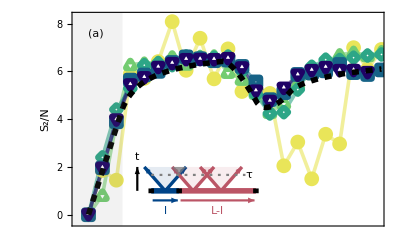

```mathematica
(* Plot the time evolution of the Renyi-2 entanglement entropy for various system sizes against the QFT prediction. *)
Fig4a=Show[ListLinePlot[Renyi2EntanglementEntropySimulatorData,PlotRange->{{-0.15,4.15},{-0.3,8.3}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{None,Style["S_2/N",Black,FontSize->15]},FrameTicks->{{{0,2,4,6,8},None},{None,None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],ListPlot[Renyi2EntanglementEntropySimulatorData,PlotMarkers->Fig4PlotMarkers],Plot[Renyi2EntanglementEntropyQFTCurve[t],{t,0,4.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All],Graphics[{Black,FontSize->15,Style[Text["(a)",{0.1,7.6}],Bold],Gray,Opacity[0.1],Rectangle[{-1,-1},{τ[25,5,1,2],9}]}],Graphics[{FontSize->15,Thickness[0.01],PlotColors[1][[1]],Line[{{0.9,1},{1.3,1}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsBlue}}],Arrow[{{1.1,1},{0.8,2}}],Arrow[{{1.1,1},{1.4,2}}],PlotColors[1][[2]],Thickness[0.01],Line[{{1.3,1},{2.4,1}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsRed}}],
Arrow[{{1.5,1},{1.2,2}}],Arrow[{{1.5,1},{1.8,2}}],Arrow[{{1.9,1},{1.6,2}}],Arrow[{{1.9,1},{2.2,2}}],
PlotColors[0.1][[2]],Triangle[{{1.5,1},{1.2,2},{1.8,2}}],Triangle[{{1.9,1},{2.2,2},{1.6,2}}],PlotColors[0.1][[1]],Triangle[{{1.1,1},{0.8,2},{1.4,2}}],Opacity[1],Thickness[0.01],Black,Line[{{0.9,0.9},{0.9,1.1}}],Line[{{1.3,0.9},{1.3,1.1}}],Line[{{2.4,0.9},{2.4,1.1}}],Gray,Opacity[0.7],Triangle[{{1.3,1.6667},{1.4,2},{1.2,2}}],Dashing[{0.005,0.01}],Opacity[1],Thickness[0.004],Line[{{0.9,1.6667},{2.25,1.6667}}],Dashing[None],Black,Thickness[0.004],Arrowheads[{{0.015,0.9,NiceArrowHeadsBlack}}],Arrow[{{0.7,1},{0.7,2}}],FontSize->13,Text["t",{0.7,2.4}],Text["τ",{2.3,1.6667}],PlotColors[1][[1]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsBlue},{0.015,0.96,NiceArrowHeadsBlue}}],Arrow[{{0.92,0.6},{1.28,0.6}}],PlotColors[1][[2]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsRed},{0.015,0.96,NiceArrowHeadsRed}}],Arrow[{{1.32,0.6},{2.38,0.6}}],PlotColors[1][[1]],Text["l",{1.1,0.15}],PlotColors[1][[2]],Text["L-l",{1.85,0.15}]}],ImageSize->{Automatic,180.3}]
```

#### (b) Renyi-2 mutual information

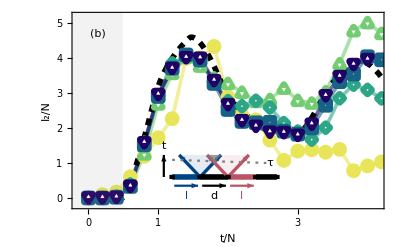

```mathematica
(* Plot the time evolution of the Renyi-2 mutual information for various system sizes against the QFT prediction. *)
Fig4b=Show[ListLinePlot[Renyi2MutualInformationSimulatorData,PlotRange->{{-0.15,4.15},{-0.2,5.2}},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->Fig4PlotStyles,FrameLabel->{Style["t/N",Black,FontSize->15],Style["I_2/N",Black,FontSize->15]},FrameTicks->{{{0,1,2,3,4,5},None},{{0,{τ[25,5,1,2],"τ/N"},1,2,3,4},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],
Plot[Renyi2MutualInformationQFTCurve[t],{t,0,4.2},PlotStyle->{{Black,Thickness[0.01],Dashed}},PlotRange->All],ListPlot[Renyi2MutualInformationSimulatorData,PlotMarkers->Fig4PlotMarkers],Graphics[{Black,FontSize->15,Style[Text["(b)",{0.13,4.7}],Bold],Gray,Opacity[0.1],Rectangle[{-1,-1},{τ[25,5,1,2],9}]}],Graphics[{FontSize->15,Thickness[0.01],PlotColors[1][[1]],Line[{{1.2,0.6},{1.6,0.6}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsBlue}}],Arrow[{{1.6,0.6},{1.3,1.23}}],Arrow[{{1.6,0.6},{1.9,1.23}}],Black,Thickness[0.01],Line[{{1.6,0.6},{2,0.6}}],Line[{{2.4,0.6},{2.7,0.6}}],PlotColors[1][[2]],Line[{{2,0.6},{2.4,0.6}}],Thickness[0.006],Arrowheads[{{0.018,0.5,NiceArrowHeadsRed}}],
Arrow[{{2,0.6},{1.7,1.23}}],Arrow[{{2,0.6},{2.3,1.23}}],
PlotColors[0.1][[2]],Triangle[{{2,0.6},{1.7,1.23},{2.3,1.23}}],PlotColors[0.1][[1]],Triangle[{{1.6,0.6},{1.3,1.23},{1.9,1.23}}],Opacity[1],Thickness[0.01],Black,Line[{{1.2,0.54},{1.2,0.66}}],Line[{{1.6,0.54},{1.6,0.66}}],Line[{{2.4,0.54},{2.4,0.66}}],Line[{{2,0.54},{2,0.66}}],Line[{{2.7,0.54},{2.7,0.66}}],FontSize->13,Gray,Opacity[0.7],Triangle[{{1.8,1},{1.9,1.23},{1.7,1.23}}],Dashing[{0.005,0.01}],Opacity[1],Thickness[0.004],Line[{{1.2,1.09},{2.55,1}}],Dashing[None],Black,Thickness[0.004],Arrowheads[{{0.015,0.9,NiceArrowHeadsBlack}}],Arrow[{{1.08,0.6},{1.08,1.23}}],Text["t",{1.08,1.48}],Text["τ",{2.6,1}],PlotColors[1][[1]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsBlue},{0.015,0.96,NiceArrowHeadsBlue}}],Arrow[{{1.23,0.35},{1.57,0.35}}],PlotColors[1][[2]],Arrowheads[{{-0.015,0.04,NiceArrowHeadsRed},{0.015,0.96,NiceArrowHeadsRed}}],Arrow[{{2.03,0.35},{2.37,0.35}}],Black,Arrowheads[{{-0.015,0.04,NiceArrowHeadsBlack},{0.015,0.96,NiceArrowHeadsBlack}}],Arrow[{{1.63,0.35},{1.97,0.35}}],Text["d",{1.8,0.065}],PlotColors[1][[1]],Text["l",{1.4,0.065}],PlotColors[1][[2]],Text["l",{2.2,0.065}]}],ImageSize->{Automatic,220}]
```

### Final figure

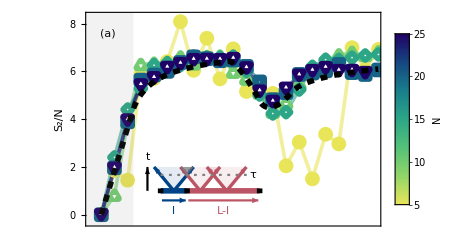
-Graphics- |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
(* Combine the latter two plots with a bar legend. *)
Fig4=Legended[Grid[{{Fig4a,,,,,,,,,,,,},{Fig4b}},Alignment->Left,Spacings->{0,0}],Placed[BarLegend[{ContinuousColors[0.8,0],{0,0.8}},LabelStyle->{Black,FontSize->12},LegendMarkerSize->160,Ticks->{{0,"5"},{0.2,"10"},{0.4,"15"},{0.6,"20"},{0.8,"25"}},LegendLabel->Style["N",FontSize->14,Black]],{1,0.607}]]
```

```mathematica
(* Compute τ/N. *)
τ[25,5,1,2]//N
```

0.487859

Fig. 5

### Data generation

#### Photonic simulator

```mathematica
(* Generate data sets. *)

(* α=2 (relativistic). *)
RenyiMISimulatorRelativisticData=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,2,1,0.1];

(* α=1.5. *)
RenyiMISimulatorFractionalα15Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,1.5,1,0.1];

(* α=1. *)
RenyiMISimulatorFractionalα1Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,1,1,0.1];

(* α=0.5. *)
RenyiMISimulatorFractionalα05Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,0.5,1,0.1];

(* α->0. *)
RenyiMISimulatorFractionalα0Data=Renyi2MutualInformationSpacetimeSimulator[0.5,0.01,20,6,0.0001,1,0.1];
```

#### Light cones

```mathematica
(* Function that selects the points of the informational wave front. *)
FitPoints[data_,modes_,threshold_]:=Module[{data2=Transpose[Partition[data,modes]]},Module[{data3=Table[SelectFirst[data2[[j]],#[[3]]>=threshold&],{j,1,Length[data2]}]},Table[{data3[[k,1]],data3[[k,2]]},{k,1,Length[data3]}]]];
```

```mathematica
(* Points to be fit. *)

(* α=2 (relativistic). *)
RenyiMISimulatorRelativisticFitPoints=FitPoints[RenyiMISimulatorRelativisticData,7,0.01];

(* α=1.5. *)
RenyiMISimulatorFractionalα15FitPoints=FitPoints[RenyiMISimulatorFractionalα15Data,7,0.01];

(* α=1. *)
RenyiMISimulatorFractionalα1FitPoints=FitPoints[RenyiMISimulatorFractionalα1Data,7,0.01];

(* α=0.5. *)
RenyiMISimulatorFractionalα05FitPoints=FitPoints[RenyiMISimulatorFractionalα05Data,7,0.01];

(* α->0. *)
RenyiMISimulatorFractionalα0FitPoints=FitPoints[RenyiMISimulatorFractionalα0Data,7,0.01];
```

#### Fits

```mathematica
(* Fit functions up to modes. *)

(* Linear. *)
ComputeLinearFit[data_,modes_]:=NonlinearModelFit[Take[data,modes],a*x+b,{a,b},x]//Normal;

(* Algebraic. *)
ComputeAlgebraicFit[data_,modes_]:=NonlinearModelFit[Take[data,modes],{c+b*(x)^a,{0.1<a<0.9,d>0}},{a,b,c,d},x,Method->"NMinimize",MaxIterations->1000]//Normal;

(* Logarithmic. *)
ComputeLogarithmicFit[data_,modes_]:=NonlinearModelFit[Take[data,modes],{a+b*Log[x+c],{b>0,c>0}},{a,b,c},x,Method->"NMinimize",MaxIterations->1000]//Normal;
```

```mathematica
(* Compute fits. *)

(* α=2 (relativistic). *)
RenyiMISimulatorRelativisticFit=ComputeLinearFit[RenyiMISimulatorRelativisticFitPoints,7]

(* α=1.5. *)
RenyiMISimulatorFractionalα15Fit=ComputeAlgebraicFit[RenyiMISimulatorFractionalα15FitPoints,7]

(* α=1. *)
RenyiMISimulatorFractionalα1Fit=ComputeAlgebraicFit[RenyiMISimulatorFractionalα1FitPoints,7]

(* α=0.5. *)
RenyiMISimulatorFractionalα05Fit=ComputeLogarithmicFit[RenyiMISimulatorFractionalα05FitPoints,7]

(* α->0. *)
RenyiMISimulatorFractionalα0Fit=ComputeLinearFit[RenyiMISimulatorFractionalα0FitPoints,7]
```

0.0546429+0.0632143 x

0.0706742+0.0675722 x^0.774829

0.088067+0.0650877 x^0.531365

NonlinearModelFit::nrnum: The objective function for model {a+b Log[c+x],{b>0,c>0}} is not a real number at {a,b,c} = {0.134799,0.0373697,0.}.

0.138783+0.0349807 Log[0.43598+x]

0.16+3.44249×10^-18 x

### Individual plots

#### (a) inset: decay of interactions

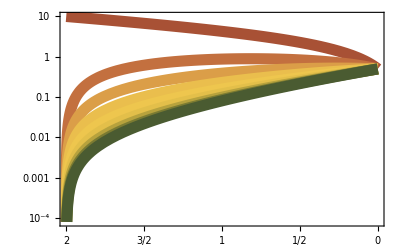

```mathematica
(* Plot of the coupling strength as a function of α for various M. *)
Fig5aInset=Show[Table[LogPlot[FractionalCoupling[20,α,0.1,j],{α,2,0},ScalingFunctions->{"Reverse",Identity},PlotTheme->"Detailed",PlotRange->{{-0.2,2.2},{0.00008,30}},PlotLegends->None,PlotStyle->{Thickness[0.02],Fig5InsetPlotColors[j-1]},FrameLabel->None,FrameTicks->{{None,{{0.0001,"10^-4"},{0.01,"10^-2"},1}},{{0,{1/2,"1/2"},1,{3/2,"3/2"},2},None}},FrameStyle->Directive[Black,Thickness[0.013]],FrameTicksStyle->Directive[Black,FontSize->9.5],GridLines->None],{j,1,9,1}],ImageSize->{Automatic,65}]
```

#### (a): Overview

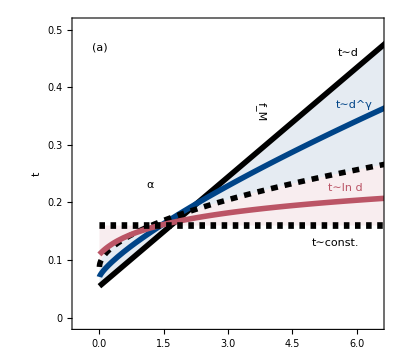

```mathematica
(* Plot the Renyi-2 mutual information in spacetime for given α. *)
Fig5a=Legended[Show[Plot[{RenyiMISimulatorRelativisticFit,RenyiMISimulatorFractionalα15Fit,RenyiMISimulatorFractionalα1Fit,RenyiMISimulatorFractionalα05Fit,RenyiMISimulatorFractionalα0Fit},{x,0,7},PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{-0.01,0.51}},PlotLegends->None,PlotStyle->{{Thickness[0.01],Black},{Thickness[0.01],PlotColors[1][[1]]},{Thickness[0.01],Black,Dashed},{Thickness[0.01],PlotColors[1][[2]]},{Thickness[0.012],Black,Dashing[{0.01,0.01}]}},Filling->{1->{{3},Directive[PlotColors[0.1][[1]]]},3->{{5},Directive[PlotColors[0.1][[2]]]}},FrameLabel->{None,Style["t",Black,FontSize->15]},FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{None,None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None,Epilog->Inset[Fig5aInset,{1.6,0.34}]],Graphics[{Black,FontSize->11,Text["α",{1.18,0.231}],Text["f_M",{3.77,0.358},Automatic,{0,-1}],FontSize->12,Text["t∼d",{5.8,0.46},Automatic,{0.5,0.43}],Text["t∼const.",{5.5,0.129}],PlotColors[1][[1]],Text["t∼d^γ",{5.95,0.37},Automatic,{0.5,0.25}],PlotColors[1][[2]],Text["t∼ln d",{5.74,0.225},Automatic,{0.5,0.05}],Black,FontSize->14,Style[Text["(a)",{0,0.47}],Bold]}],AspectRatio->0.9,ImageSize->{Automatic,190}],Placed[BarLegend[{Fig5InsetPlotColors,{0,8}},LabelStyle->{Black,FontSize->7},LegendLayout->"Row",LegendMarkerSize->{70,10},Ticks->{0,2,4,6,8},LegendLabel->Placed[Style["M",FontSize->8,Black],Right]],{0.290,0.93}]]
```

#### (b): α=2

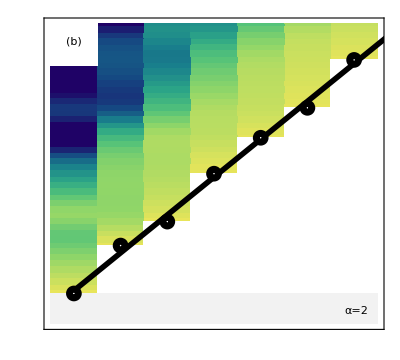

```mathematica
(* α=2 (relativistic). *)
Fig5b=Show[ListDensityPlot[RenyiMISimulatorRelativisticData,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->None,FrameTicks->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorRelativisticFitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorRelativisticFitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(b)",{0,0.47}],Bold],FontSize->12,Text["α=2",{6.05,0.02}]}],Plot[RenyiMISimulatorRelativisticFit,{x,0,7},PlotStyle->{Black,Thickness[0.01]}],ListPlot[RenyiMISimulatorRelativisticFitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,Black,1,1]],AspectRatio->0.9,ImageSize->{Automatic,183}]
```

#### (c): α=1.5

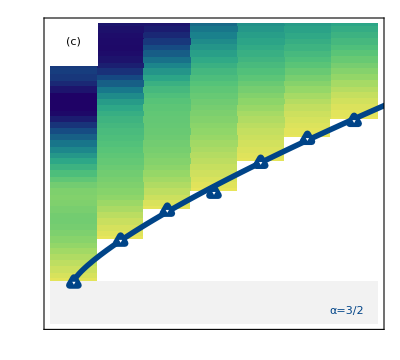

```mathematica
(* α=1.5 *)
Fig5c=Show[ListDensityPlot[RenyiMISimulatorFractionalα15Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->None,FrameTicks->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα15FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα15FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(c)",{0,0.47}],Bold],PlotColors[1][[1]],FontSize->12,Text["α=3/2",{5.85,0.02}]}],Plot[RenyiMISimulatorFractionalα15Fit,{x,0,7},PlotStyle->{PlotColors[1][[1]],Thickness[0.01]}],ListPlot[RenyiMISimulatorFractionalα15FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,PlotColors[1][[1]],1,2]],AspectRatio->0.9,ImageSize->{Automatic,183}]
```

#### (d): α=1

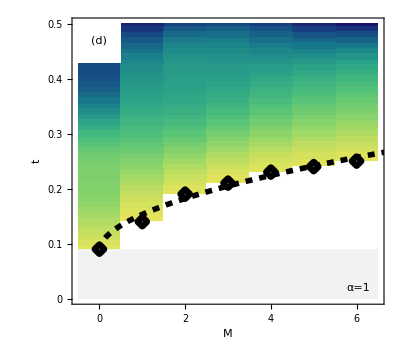

```mathematica
(* α=1. *)
Fig5d=Show[ListDensityPlot[RenyiMISimulatorFractionalα1Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->{Style["M",Black,FontSize->15],Style["t",Black,FontSize->15]},FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{{0,1,2,3,4,5,6},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα1FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα1FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(d)",{0,0.47}],Bold],FontSize->12,Text["α=1",{6.05,0.02}]}],Plot[RenyiMISimulatorFractionalα1Fit,{x,0,7},PlotStyle->{Black,Thickness[0.01],Dashed}],ListPlot[RenyiMISimulatorFractionalα1FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,Black,1,3]],AspectRatio->0.9,ImageSize->{Automatic,227}]
```

#### (e): α=0.5

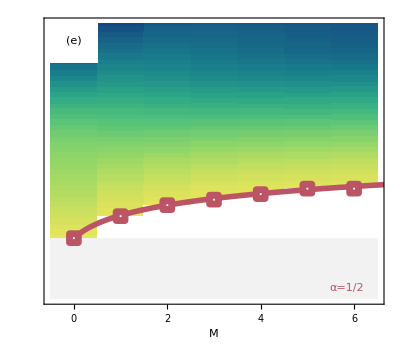

```mathematica
(* α=0.5. *)
Fig5e=Show[ListDensityPlot[RenyiMISimulatorFractionalα05Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->{Style["M",Black,FontSize->15]},FrameTicks->{{None,None},{{0,1,2,3,4,5,6},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα05FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα05FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(e)",{0,0.47}],Bold],PlotColors[1][[2]],FontSize->12,Text["α=1/2",{5.85,0.02}]}],Plot[RenyiMISimulatorFractionalα05Fit,{x,0,7},PlotStyle->{Thickness[0.01],PlotColors[1][[2]]}],ListPlot[RenyiMISimulatorFractionalα05FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,PlotColors[1][[2]],1,4]],AspectRatio->0.9,ImageSize->{Automatic,223.8}]
```

#### (f): α→0

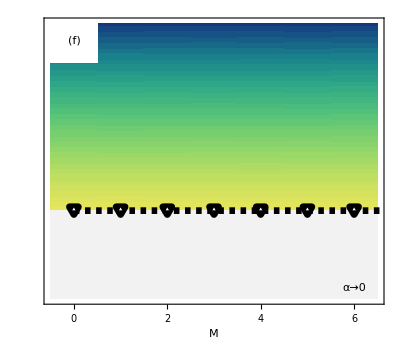

```mathematica
(* α->0. *)
Fig5f=Show[ListDensityPlot[RenyiMISimulatorFractionalα0Data,PlotTheme->"Detailed",PlotRange->{{-0.5,6.5},{0,0.5}},PlotLegends->None,ColorFunction->ContinuousColors[0.2,0.01],ColorFunctionScaling->False,InterpolationOrder->0,FrameLabel->{Style["M",Black,FontSize->15]},FrameTicks->{{None,None},{{0,1,2,3,4,5,6},None}},FrameStyle->Directive[Black,Thickness[0.005]],FrameTicksStyle->Directive[Black,FontSize->14],GridLines->None],GenerateWhiteRegion[RenyiMISimulatorFractionalα0FitPoints],Graphics[{Gray,Opacity[0.1],Rectangle[{-0.5,0},{6.5,RenyiMISimulatorFractionalα0FitPoints[[1,2]]}],Opacity[1],White,Rectangle[{-0.5,0.43},{0.5,0.55}],Black,FontSize->14,Style[Text["(f)",{0,0.47}],Bold],FontSize->12,Text["α→0",{6,0.02}]}],Plot[RenyiMISimulatorFractionalα0Fit,{x,0,7},PlotStyle->{Black,Thickness[0.012],Dashing[{0.01,0.01}]}],ListPlot[RenyiMISimulatorFractionalα0FitPoints,PlotMarkers->NicePlotmarkers[9,0.3,White,Black,1,5]],AspectRatio->0.9,ImageSize->{Automatic,223.8}]
```

### Final figure

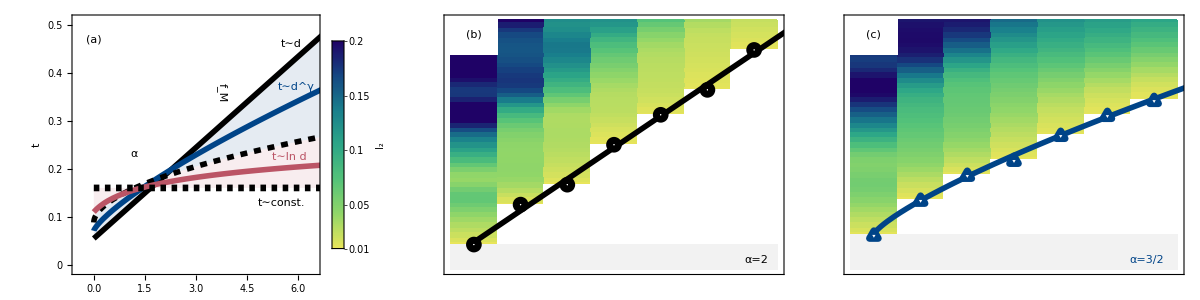
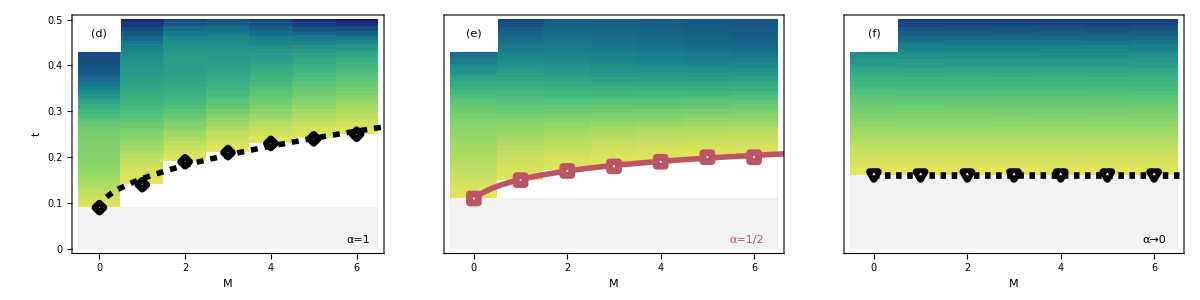
-Graphics- |  |  |  |  |  |  | 
-Graphics- |  |  |  |  |  |  |

```mathematica
(* Combine the latter six figures. *)
Fig5=Legended[Grid[{{Grid[{{Fig5a,Fig5b,Fig5c}},Alignment->Center,Spacings->0.8],,,,,,,},{Grid[{{Fig5d,Fig5e,Fig5f}},Alignment->Bottom,Spacings->0.8]}},Alignment->Left],Placed[BarLegend[{ContinuousColors[0.2,0.01],{0.01,0.2}},LabelStyle->{Black,FontSize->12},LegendMarkerSize->160,Ticks->{{0.01,"0.01"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"},{0.2,"0.2"}},LegendLabel->Style["I_2",FontSize->14,Black]],{0.99,0.598}]]
```